# ECH 28GHz Perpendicular Stratification, B(x)ẑ Linear gradient in B(x): 0.7T ≤ B ≤ 1.3T n_e=0.2×10^19=const n_z=0.2 T_e=1.0 KeV

## To use this notebook:

### Get dispersion routines by evaluating Plasma_Dispersion.nb Get plotting and printing routines by evaluating PlotPack.nb These notebooks are in github : https://github.com/ORNL-Fusion/dispersioneering-Mathematica/Plasma_Dispersion_Utilities Note: Slab profile models are defined in initialization cells at the bottom of this notebook. Note: Input parameters are set in initialization cells below case runs. To change parameters edit initialization cells near bottom of this notebook.

## Plot Real and Imaginary parts of n_x from 4nd order cold plasma dispersion relation (Plus and Minus roots)

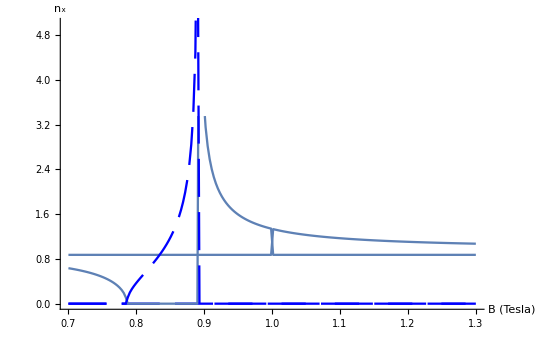

dataSet=Perpendicular Stratification 28GHz, grad B

xProfileMin=0.7

xProfileMax=1.3

nXmin=2.×10^18

nXmax=2.×10^18

BXmin=0.7

BXmax=1.3

freq=28000.

nz=0.2

etaList={0.,1.,0.,0.,0.}

xmin=0.7

xmax=1.3

```mathematica
nPerpPM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
nxColdDisPM[freq,ne,b,nz,etaList]];
ntPM=Table[Flatten[{x,nPerpPM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[ntPM]⟦1⟧,Transpose[ntPM]⟦2⟧}];
nM=Transpose[{Transpose[ntPM]⟦1⟧,Transpose[ntPM]⟦3⟧}];
g1=PPComplexListPlot[nP,"B (Tesla)","n_x"];
g2=PPComplexListPlot[nM,"B (Tesla)","n_x"];
Show[{g1,g2},PlotRange->{0.,5.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_x from 4nd order cold plasma dispersion relation (Fast and Slow roots)

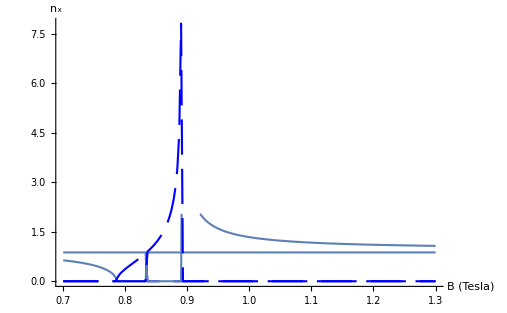

dataSet=Perpendicular Stratification 28GHz, grad B

xProfileMin=0.7

xProfileMax=1.3

nXmin=2.×10^18

nXmax=2.×10^18

BXmin=0.7

BXmax=1.3

freq=28000.

nz=0.2

etaList={0.,1.,0.,0.,0.}

xmin=0.7

xmax=1.3

```mathematica
nPerpFS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
nxColdDisFS[freq,ne,b,nz,etaList]];
ntFS=Table[Flatten[{x,nPerpFS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[ntFS]⟦1⟧,Transpose[ntFS]⟦2⟧}];
nS=Transpose[{Transpose[ntFS]⟦1⟧,Transpose[ntFS]⟦3⟧}];
g1=PPComplexListPlot[nF,"B (Tesla)","n_x"];
g2=PPComplexListPlot[nS,"B (Tesla)","n_x"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

## Now Warm Plasma Stuff

### Plot Real and Imaginary parts of nx from 6th order warm plasma dispersion relation (expanded to 2nd order in k_⌊ρ)

dataSet=Perpendicular Stratification 28GHz, grad B

xProfileMin=0.7

xProfileMax=1.3

nXmin=2.×10^18

nXmax=2.×10^18

BXmin=0.7

BXmax=1.3

TXmin=1.

TXmax=1.

freq=28000.

nz=0.2

etaList={0.,1.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={1,1,0,0,0,0}

xmin=0.7

xmax=1.3

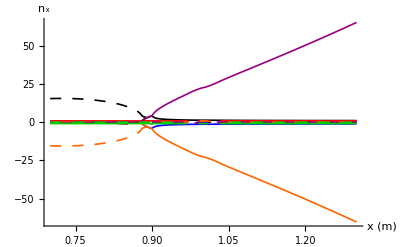

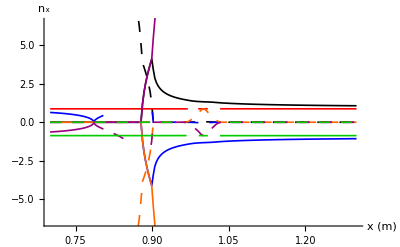

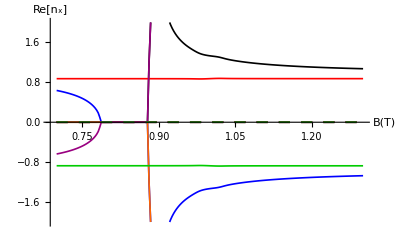

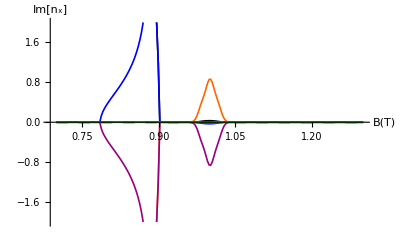

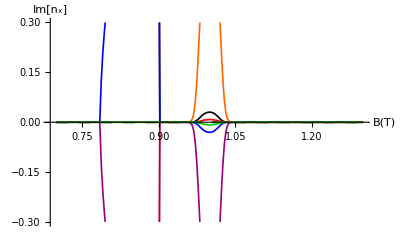

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},
		x0=x;
     ne=nprof[x0];
b=bprof[x0];
	  TL=tprof[x0] *TList;
	  WarmDis6[freq,ne,b,nz,etaList,TL]]

nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

g6=ComplexVectorListPlot[roots,"x (m)","n_x"];
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,TXmin, TXmax, freq,nz,etaList,TList, modelList,xmin,xmax}];
Show[g6,PlotRange->All]
Show[g6,PlotRange->{-6.5,6.5}]
ComplexVectorListPlot[rootsRe,"B(T)", "Re[n_x]", PlotRange->{-2.,2.}]
ComplexVectorListPlot[rootsIm, "B(T)", "Im[n_x]", PlotRange->{-2.,2.}]
ComplexVectorListPlot[rootsIm, "B(T)", "Im[n_x]", PlotRange->{-0.3,0.3}]
```

## Look closer to cyclotron resonance B(x): 0.95T ≤ B ≤ 1.05T

### Plot Real and Imaginary parts of nx from 6th order warm plasma dispersion relation (expanded to 2nd order in k_⌊ρ)

dataSet=Perpendicular Stratification 28GHz, grad B

xProfileMin=0.95

xProfileMax=1.05

nXmin=2.×10^18

nXmax=2.×10^18

BXmin=0.95

BXmax=1.05

TXmin=1.

TXmax=1.

freq=28000.

nz=0.2

etaList={0.,1.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={1,1,0,0,0,0}

xmin=0.95

xmax=1.05

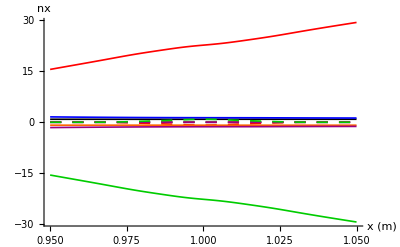

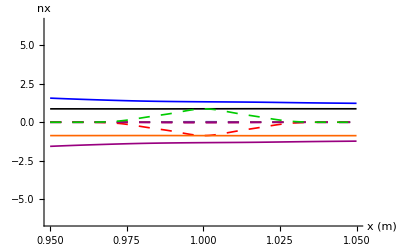

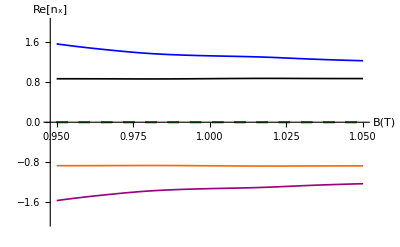

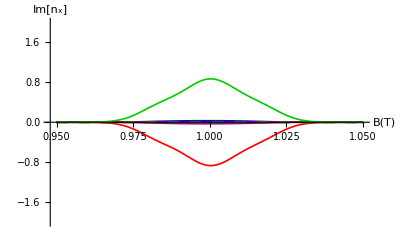

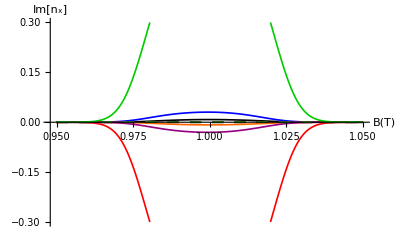

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},
		x0=x;
     ne=nprof[x0];
b=bprof[x0];
	  TL=tprof[x0] *TList;
	  WarmDis6[freq,ne,b,nz,etaList,TL]]

nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

g6=ComplexVectorListPlot[roots,"x (m)","nx"];
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,TXmin, TXmax, freq,nz,etaList,TList, modelList,xmin,xmax}];
Show[g6,PlotRange->All]
Show[g6,PlotRange->{-6.5,6.5}]
ComplexVectorListPlot[rootsRe,"B(T)", "Re[n_x]", PlotRange->{-2.,2.}]
ComplexVectorListPlot[rootsIm, "B(T)", "Im[n_x]", PlotRange->{-2.,2.}]
ComplexVectorListPlot[rootsIm, "B(T)", "Im[n_x]", PlotRange->{-0.3,0.3}]
```

### Find out which mode is which

```mathematica
nPerpWarm6[1.001]
```

{0.873522+0.0079708 ⅈ,1.32946+0.0302298 ⅈ,22.7458-0.866655 ⅈ,-0.873522-0.0079708 ⅈ,-1.32946-0.0302298 ⅈ,-22.7458+0.866655 ⅈ}

root 1 is O - mode,  root 2 is X - mode,  root 3 is Bernstein mode

#### Compare to damp_fund _ECH (RAYS fortran) weak damping approximation

At B=1.001T damp_fund_ECH gives:
 Im{n_x}=0.0305188 for X-Mode 
          Im{n_x}=0.0079274 for O-Mode
Pretty good

## Optical depth

X - mode

```mathematica
kiXModeVec=Transpose[{Transpose[nxwarm][[1]],k0*Im[Transpose[nxwarm][[3]]]}];
α=TrapezInt[kiXModeVec]
1-Exp[-2α]
```

0.631428

0.717155

damp_fund _ECH fortran gives α → 0.6505   Pretty good

O - mode

```mathematica
kiXModeVec=Transpose[{Transpose[nxwarm][[1]],k0*Im[Transpose[nxwarm][[2]]]}];
α=TrapezInt[kiXModeVec]
1-Exp[-2α]
```

0.162677

0.277728

damp_fund _ECH fortran gives α →  0.162564    Pretty good

#### Check Γ=1/2(k_x ρ_s)^2

```mathematica
Warmgamma[freq,bprof[1.],nPerpWarm6[1.001][[1]],TList](* O-Mode *)
Warmgamma[freq,bprof[1.],nPerpWarm6[1.001][[2]],TList](* X-Mode *)
Warmgamma[freq,bprof[1.],nPerpWarm6[1.001][[3]],TList] (* Bernstein-Mode *)
```

{0.0014939+0.0000272656 ⅈ,2.7428+0.0500597 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{0.0034589+0.000157381 ⅈ,6.35054+0.288951 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{1.01154-0.0771949 ⅈ,1857.19-141.73 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

#### Man! It looks like the small k_x ρ_s expansion is never going to be valid for the Bernstein mode except very near the conversion point. Look a little closer to conversion point

```mathematica
nPerpWarm6[0.92]
```

{0.871856,2.03379,10.2653,-0.871856,-2.03379,-10.2653}

Check Γ=1/2(k_x ρ_s)^2

```mathematica
Warmgamma[freq,bprof[0.92],nPerpWarm6[0.92][[1]],TList](* O-Mode *)
Warmgamma[freq,bprof[0.92],nPerpWarm6[0.92][[2]],TList](* X-Mode *)
Warmgamma[freq,bprof[0.92],nPerpWarm6[0.92][[3]],TList] (* Bernstein-Mode *)
```

{0.00175843,3.22847,0.,0.,0.,0.}

{0.00956857,17.5679,0.,0.,0.,0.}

{0.243767,447.556,0.,0.,0.,0.}

#### Still not all that small

## Plot Profiles

```mathematica
Plot[nprof[x],{x,xmin,xmax}]
```

-Graphics-

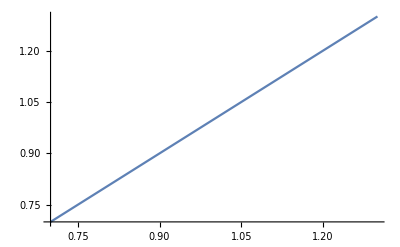

```mathematica
Plot[bprof[x],{x,xmin,xmax}]
```

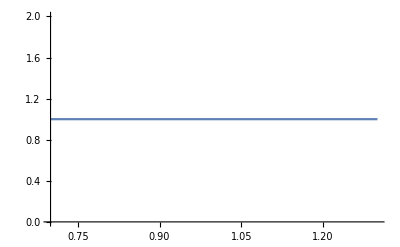

```mathematica
Plot[tprof[x],{x,xmin,xmax}]
```

```mathematica
αHcut[BXmax,freq, nz,1]
```

0.960125

## Initialization

## Set Perpendicular Parameters

### Geometric Parameters

```mathematica
xProfileMin=0.95;
xProfileMax=1.05;
nXmin=.02  10^20; 
nXmax=.02  10^20;
BXmin=0.95;
BXmax=1.05;
(* N.B. For Linear slab model Te Xmin and Te Xmax are defined here.  TList below gives the ratio of various Ti to Te  *)
TXmin=1.;
TXmax=1.;
```

### Plot Parameters

```mathematica
dataSet="Perpendicular Stratification 28GHz, grad B";
xmin=xProfileMin;
xmax=xProfileMax;
nPoints=200;
```

### RF Parameters (freq is MHz)

```mathematica
freq=28.*10^3;
c=2.9979 10^8;
k0=(2 N[π] freq 10^6)/c
nz  =0.2;
kz= nz * k0
```

586.841

117.368

### Plasma Parameters

```mathematica
etaList=Table[0.,{i,1,5}];
etaList⟦1⟧=0.;
etaList⟦2⟧=1.0;(* ion species is deuterium *)
etaList⟦3⟧=0.; 
etaList⟦4⟧=0.;etaList⟦5⟧=0.;

(* N.B. For Linear slab model Te Xmin and Te Xmax are defined above.  TList here gives the ratio of various Ti to Te (i.e. TList[[1]] = 1.0 always)  *)
TList=Table[0.,{i,1,6}];
TList⟦1⟧=1.0;TList⟦2⟧=1.0;
TList⟦3⟧=0. ;TList⟦4⟧=0.;
TList⟦5⟧=0.;TList⟦6⟧=0.;

modelList =Table[0,{i,1,6}];
modelList[[1]]=1; modelList[[2]]=1
modelList[[3]]=0; modelList[[4]]=0;
modelList[[5]]=0; modelList[[6]]=0;

nminList=Table[0.,{i,1,6}];
nminList⟦1⟧=-1;nminList⟦2⟧=-2;
nminList⟦3⟧=-2;nminList⟦4⟧=-2;
nminList⟦5⟧=-2;nminList⟦6⟧=-2;

nmaxList=Table[0.,{i,1,6}];
nmaxList⟦1⟧=1;nmaxList⟦2⟧=2;
nmaxList⟦3⟧=2;nmaxList⟦4⟧=2;
nmaxList⟦5⟧=2;nmaxList⟦6⟧=2;
```

1

## Magnetic field,Density and Temperature Profiles

```mathematica
bprof[x_]:=If[Abs[(BXmax-BXmin)/BXmax]>10^-6,BXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(BXmax-BXmin),BXmin];
```

```mathematica
nprof[x_]:=If[Abs[(nXmax-nXmin)/nXmax]>10^-6,nXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(nXmax-nXmin),nXmin];
```

```mathematica
tprof[x_]:=If[Abs[(TXmax-TXmin)/TXmax]>10^-6,TXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(TXmax-TXmin),TXmin];
```

```mathematica
αHcut[B_,freq_, nz_,sgn_]:=(1-nz^2)×(1+sgn*2.79926 B/freq)
```

## Trapezoidal Rule List Integral

```mathematica
TrapezInt[v_List]:=

(* Integral using trapezoidal rule of a list of {x,f(x)} pairs.
	v is a list of the form {{x1,f(x1)},{x2,f(x2)},...}  	*)
	
	Module[{int=0},
	Do[int=int+(v[[i+1,1]]-v[[i,1]])*(v[[i+1,2]]+v[[i,2]])/2.,
	{i,1,Length[v]-1}];
	int]
```